# Лабораторная работа №2

## Линейные математические модели колебательных явлений

Мат. моделирование динамических процессов 1
БГУ, ММФ, 3 курс, 6 семестр
специальность Компьютерная математика и системный анализ
февраль 2022
ММФ, КМ и СА, доц. Лаврова О.А., доц. Щеглова Н.Л.
работу выполнил 
студент 3 курса 5 группы ММФ БГУ
Кирилло Дмитрий

## Объект моделирования -- пружинный осциллятор

### Концептуальная постановка задачи

Объектом исследования является физическое тело массы m, которое находится на одном конце пружины, второй конец пружины жестко закреплен. Тело имеет небольшие размеры по сравнению с длиной пружины, поэтому принимаем его за материальную точку.

Тело движется вперед или назад по горизонтальной поверхности. Обозначим через r(t) координату тела вдоль оси пружины относительно положения равновесия r=0, когда пружина не сжата и не растянута. Будем считать, что r(t)>0, когда пружина растянута и r(t)<0, когда она сжата.

Расстояние между положением равновесия  r=0 и стенкой, к которой крепится пружина, равно  L.

Тело находится под действием силы упругости пружины. Сила упругости описывается законом Гука F=-k r, где коэффициент упругости k=const>0. Закон Гука является экспериментальным и справедлив при небольших отклонениях пружины от ее положения равновесия.

Можно сделать допущение, что тело движется без трения. Предположение об отсутствии трения справедливо для небольших промежутков времени. Если учитывать сопротивление среды, то можно полагать, что сила трения пропорциональна скорости движения F_тр=-μ (ⅆr(t))/ⅆt с коэффициентом трения μ=const>0. Приведенная зависимость называется формулой Стокса и является допустимой при малых скоростях движения.

На тело может действовать внешняя сила, например F=F_0 sin(t ω_2).

Принимая во внимание, что в момент времени t=0 пружину растянули на величину r_0 и сообщили телу скорость v_0, требуется определить координату тела r(t) как функцию времени.

## Задание 1. Гармонические колебания

Математическая модель пружинного осциллятора без учета сопротивления среды представляет собой задачу Коши для линейного однородного дифференциального уравнения второго порядка с постоянными коэффициентами следующего вида

(ⅆ^2 r(t))/(ⅆ t^2)+ω^2 r(t)==0, 
r(0)=r_0,
(ⅆr(0))/ⅆt=v_0,

где ω=√(k/m)=const>0 -- собственная частота колебаний.

### Задание 1.1 (Амплитуда колебаний)

Найдите условия на величины начальных данных r_0 и v_0, при выполнении которых груз не может удариться о стенку. , равно  L. Для этого необходимо найти аналитическое решение математической модели (1) в виде r(t)=A cos(t ω+ϕ_0) и сформулировать условие A≤L. Здесь L -- это расстояние между положением равновесия  r≡0 и стенкой, к которой крепится пружина.

Найденное условие задает ограничения на применимость математической модели (1), так как при соударении со стеной тело испытывает дополнительную силу, которая должна быть учтена в математической модели.

Задание сформулировано на основе материала из [1, стр. 34, упр. 4].

```mathematica
DSolve[{r''[t]+ω^2 r[t]==0,r[0]==r0,r'[0]==v0},r[t],t]//Simplify
```

{{r[t]→r0 Cos[t ω]+(v0 Sin[t ω])/ω}}

Так как ω=√(k/m)=const>0, то  диф. уравнение второго порядка (ⅆ^2 r(t))/(ⅆ t^2)+ω^2 r(t)==0 можно переписать в следующем виде:
m (ⅆ^2 r(t))/(ⅆ t^2)+k r(t)==0 (домножая ДУ на m,знаменатель второго слагаемого можно убрать, так как у нас,по условию,  ω>0, соответственно m также будет больше нуля)

```mathematica
DSolve[{m r''[t]+k r[t]==0,r[0]==r0,r'[0]==v0},r[t],t]//Simplify
```

{{r[t]→r0 Cos[(√k t)/(√m)]+(√m v0 Sin[(√k t)/(√m)])/(√k)}}

```mathematica
(*некоторое рассуждение и предположение*)
Solve[Equal[A Cos[(t w) + f0],(DSolve[{r''[t]+w^2 r[t]==0,r[0]==r0,r'[0]==v0},r[t],t]//Values)],A]//Expand
Solve[Equal[A Cos[(t w) + f0],(DSolve[{r''[t]+w^2 r[t]==0,r[0]==r0,r'[0]==v0},r[t],t]//Values)],f0]//Expand
```

{{A→r0 Cos[t w] Sec[f0+t w]+(v0 Sec[f0+t w] Sin[t w])/w}}

{{f0→ConditionalExpression[-t w-ArcCos[(r0 w Cos[t w]+v0 Sin[t w])/(A w)]+2 π C[1], C[1]∈ℤ]},{f0→ConditionalExpression[-t w+ArcCos[(r0 w Cos[t w]+v0 Sin[t w])/(A w)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Block[{r=A Cos[t ω + Subscript[ϕ, 0]]},
Solve[(r/.{t->0})==r0 && (D[r,t]/.{t->0})==v0,{A,Subscript[ϕ, 0]}]//Simplify
]
```

{{A→-(√(v0^2+r0^2 ω^2))/ω,ϕ_0→ConditionalExpression[ArcTan[-(r0 ω)/(√(v0^2+r0^2 ω^2)),v0/(√(v0^2+r0^2 ω^2))]+2 π C[1], C[1]∈ℤ]},{A→(√(v0^2+r0^2 ω^2))/ω,ϕ_0→ConditionalExpression[ArcTan[(r0 ω)/(√(v0^2+r0^2 ω^2)),-v0/(√(v0^2+r0^2 ω^2))]+2 π C[1], C[1]∈ℤ]}}

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory"
```

D:\ММДС

```mathematica
Import["LR2T1.pdf",{"PageImages",1}]
```

-Graphics-

### Задание 1.2 (Динамическая визуализация с учетом соударения тела о стенку)

Осуществите динамическую визуализацию поведения пружинного осциллятора с возможностью интерактивного задания параметров модели ω, r_0, v_0, L. 

В случае соударения со стеной, к которой крепится пружина, остановите анимацию, используя выражение WhenEvent функции NDSolve или опцию Method (значение EventLocator) функции NDSolve .

Справочную информацию можно найти по ссылкам 
https://reference.wolfram.com/language/ref/WhenEvent.html
.

```mathematica
Quiet@Manipulate[{{TextCell[
If[√(r0^2+(m v0^2)/k)<L,StringForm["r_0^2= ``<`` =L",NumberForm[√(r0^2+(m v0^2)/k),2],NumberForm[L,2]],
StringForm["r_0^2=`` ≥ `` =L",NumberForm[√(r0^2+(m v0^2)/k),2],NumberForm[L,2]]],
"Output"]},
{Animate[Show[
Graphics[{Line[{{-√(r0^2+(m v0^2)/k),0},{Max[√(r0^2+(m v0^2)/k),L],0}}],Line[{{L,-0.7},{L,0.7}}]},ImageSize->300],Graphics[{Thickness[0.01],Blue,Line[{{-√(r0^2+(m v0^2)/k)-2,0},{sol[t],0}}],Red,PointSize[Large],Point[{sol[t],0}]}]],{t,0,sol⟦1,1,-1⟧}]}},
{{m,0.5,"m"},0.01,1,0.01,Appearance->"Labeled"},
{{k,1,"k"},0.01,1,0.01,Appearance->"Labeled"},
{{r0,0,"r_0"},-1,1,0.01,Appearance->"Labeled"},
{{v0,0,"v_0"},-1,1,0.01,Appearance->"Labeled"},
{{L,2},2,4,0.1,Appearance->"Labeled"},
Button["Refresh data",sol=r/.(NDSolve[{m r''[t]+k r[t]==0,r[0]==r0,r'[0]==v0},r,{t,0,2π },Method->{"EventLocator","Event"->r[t]-L}]⟦1,1⟧);
]
]
```

Part::partd: Part specification sol⟦1,1,-1⟧ is longer than depth of object.

Animate::vsform: Animate argument {t,0,sol⟦1,1,-1⟧} does not have the correct form for a variable specification.

Part::partd: Part specification sol⟦1,1,-1⟧ is longer than depth of object.

Animate::vsform: Animate argument {t,0,sol⟦1,1,-1⟧} does not have the correct form for a variable specification.

## Задание 2. Колебания с учетом сопротивления среды

Полагаем, что на пружинный осциллятор воздействует сила трения, заданная формулой Стокса  F_тр=-μ (ⅆr(t))/ⅆt, где коэффициент трения μ=const>0.

Математическая модель пружинного осциллятора c учетом сопротивления среды представляет собой задачу Коши для линейного однородного дифференциального уравнения второго порядка с постоянными коэффициентами следующего вида

m(ⅆ^2 r(t))/(ⅆ t^2)==-k r(t)-μ(ⅆr(t))/ⅆt , 
r(0)=r_0,
(ⅆr(0))/ⅆt=v_0.

### Задание 2.1 (Качественный анализ по фазовому портрету)

Изобразите фазовые траектории для модели (2) для трех возможных типов поведения системы: затухающее колебание, критическое колебание, апериодическое затухание. 

Для каждого типа поведения проанализируйте  характер положения равновесия r(t)≡0,  v(t)≡0 (узел, седло, фокус, центр или др.)   и его устойчивость по фазовому портрету.

```mathematica
DSolve[{m r''[t]==-(k r[t])-(μ r'[t]),r[0]==r0,r'[0]==v0},r[t],t]
```

{{r[t]→1/(2 √(-4 k m+μ^2))(-2 ⅇ^(1/2 t (-μ/m-(√(-4 k m+μ^2))/m)) m v0+2 ⅇ^(1/2 t (-μ/m+(√(-4 k m+μ^2))/m)) m v0-ⅇ^(1/2 t (-μ/m-(√(-4 k m+μ^2))/m)) r0 μ+ⅇ^(1/2 t (-μ/m+(√(-4 k m+μ^2))/m)) r0 μ+ⅇ^(1/2 t (-μ/m-(√(-4 k m+μ^2))/m)) r0 √(-4 k m+μ^2)+ⅇ^(1/2 t (-μ/m+(√(-4 k m+μ^2))/m)) r0 √(-4 k m+μ^2))}}

```mathematica
DSolve[{m r''[t]==-(k r[t])-(μ r'[t]),r[0]==r0,r'[0]==v0},r[t],t]//Simplify//Flatten
```

{r[t]→(ⅇ^(-(t (μ+√(-4 k m+μ^2)))/(2 m)) (2 (-1+ⅇ^((t √(-4 k m+μ^2))/m)) m v0+(-1+ⅇ^((t √(-4 k m+μ^2))/m)) r0 μ+(1+ⅇ^((t √(-4 k m+μ^2))/m)) r0 √(-4 k m+μ^2)))/(2 √(-4 k m+μ^2))}

Устойчивый фокус (асимптотическая устойчивость) : 
μ = 3, k = 2,  m = 4:  μ^2 - 4km < 0

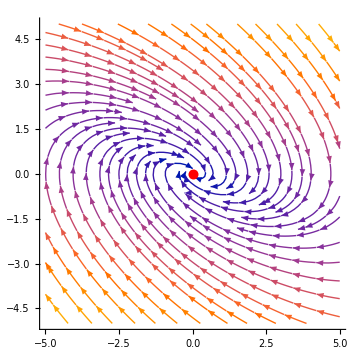

```mathematica
Show[Graphics[{Red,PointSize[0.02],Point[{0,0}]}],
StreamPlot[{y,-2/4 x-3/4 y},{x,-5,5},{y,-5,5}],Axes->True,ImageSize->Medium]
```

Устойчивый  узел (асимптотическая устойчивость) : 
μ = 4, k = 2,  m = 2:  μ^2 - 4km = 0

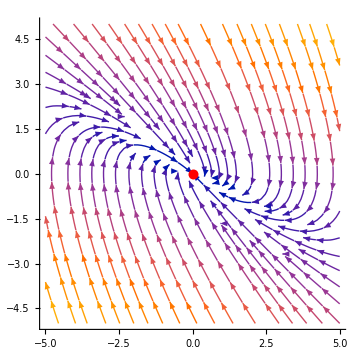

```mathematica
Show[Graphics[{Red,PointSize[0.02],Point[{0,0}]}],
StreamPlot[{y,-x-2y},{x,-5,5},{y,-5,5}],Axes->True,ImageSize->Medium]
```

Устойчивый узел (асимптотическая устойчивость) : 
μ = 5, k = 1,  m = 2:  μ^2 - 4km > 0

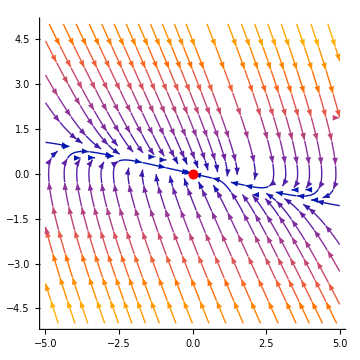

```mathematica
Show[Graphics[{Red,PointSize[0.02],Point[{0,0}]}],
StreamPlot[{y,-1/2 x-5/2 y},{x,-5,5},{y,-5,5}],Axes->True,ImageSize->Medium]
```

### Задание 2.2 (Качественный анализ по теореме Ляпунова)

Определите собственные значения матрицы динамической системы, соответствующей математической модели (2). 

По собственным значениям проанализируйте  характер положения равновесия r(t)≡0,  v(t)≡0 (узел, седло, фокус, центр или др.) и его устойчивость для различных типов поведения системы: затухающее колебание, критическое колебание, апериодическое затухание.

Найдем собственные значения матрицы динамической системы, соответствующей математической модели (2):

```mathematica
Import["LR2T2.2.pdf",{"PageImages",1}]
```

-Graphics-

Определим при помощи ниже написанной функции, которая была получена из решения показанном выше, по собственным значениям  характер положения равновесия r(t)≡0,  v(t)≡0  и его устойчивость для различных типов поведения системы:

```mathematica
ClearAll[Analys];
Analys[μ_,k_,m_]:={(-μ/m-Sqrt[(-μ/m)^2-4 k/m])/2,(-μ/m+Sqrt[(-μ/m)^2-4 k/m])/2}
```

Устойчивый фокус : 
μ = 3, k = 2,  m = 4:  μ^2 - 4km < 0

```mathematica
Analys[3,2,4]//N
```

{-0.375-0.599479 ⅈ,-0.375+0.599479 ⅈ}

```mathematica
Solve[Det[({{-λ, 1}, {-1/2, -3/4-λ}})]==0,λ]//N
```

{{λ→-0.375-0.599479 ⅈ},{λ→-0.375+0.599479 ⅈ}}

Так как вещественная часть λ_1 и λ_2 меньше нуля,а также равны между собой,то положение равновесия является устойчивым фокусом

Устойчивый  узел (асимптотическая устойчивость) : 
μ = 4, k = 2,  m = 2:  μ^2 - 4km = 0

```mathematica
Analys[4,2,2]//N
```

{-1.,-1.}

```mathematica
Solve[Det[({{-λ, 1}, {-1, -2-λ}})]==0,λ]
```

{{λ→-1},{λ→-1}}

Так как λ_1 и λ_2 равны между собой и меньше нуля,то положение равновесия является устойчивый  узел

Устойчивый узел (асимптотическая устойчивость): 
μ = 5, k = 1,  m = 2:  μ^2 - 4km > 0

```mathematica
Analys[5,1,2]//N
```

{-2.28078,-0.219224}

```mathematica
Solve[Det[({{-λ, 1}, {-1/2, -5/2-λ}})]==0,λ]//N
```

{{λ→-2.28078},{λ→-0.219224}}

Так как λ_1 и λ_2 меньше нуля,то положение равновесия является устойчивый узел

### Задание 2.3 (Анализ частных случаев)

Проанализируйте, какому типу поведения соответствует движение пружинного осциллятора (m=10 кг, k=10 Н/м) в воздухе (μ=1.82*10^-5 Нс/м^2), в воде (μ=1.002*10^-3 Нс/м^2), в глицерине (μ=1.49 Нс/м^2)? 
Приведенные значения для коэффициента трения  μ соответствуют температуре 20^оС.

```mathematica
(DSolve[{10 r''[t]==-(10 r[t])-(μ r'[t]),r[0]==r0,r'[0]==v0},r[t],t]/.#)&/@{{μ->1.82*10^-5},{μ->1.002*10^-3},{μ->1.49}}//Simplify
```

{{{r[t]→ⅇ^((-9.1×10^-7-1. ⅈ) t) (((0.5+4.55×10^-7 ⅈ)+(0.5-4.55×10^-7 ⅈ) ⅇ^((0.+2. ⅈ) t)) r0+((0.+0.5 ⅈ)-(0.+0.5 ⅈ) ⅇ^((0.+2. ⅈ) t)) v0)}},{{r[t]→ⅇ^((-0.0000501-1. ⅈ) t) (((0.5+0.00002505 ⅈ)+(0.5-0.00002505 ⅈ) ⅇ^((0.+2. ⅈ) t)) r0+((-3.38813×10^-21+0.5 ⅈ)+(3.38813×10^-21-0.5 ⅈ) ⅇ^((0.+2. ⅈ) t)) v0)}},{{r[t]→ⅇ^((-0.0745-0.997221 ⅈ) t) (((0.5+0.0373538 ⅈ)+(0.5-0.0373538 ⅈ) ⅇ^((0.+1.99444 ⅈ) t)) r0+((0.+0.501393 ⅈ)-(0.+0.501393 ⅈ) ⅇ^((0.+1.99444 ⅈ) t)) v0)}}}

Определяем знак через μ^2-4km. Так как, по условию задания,  m=10 кг, k= 10 Н/м, то получаем:
μ^2-400. 
Подставим значения μ и определим тип поведения движения пружинного осциллятора.

В воздухе (μ=1.82*10^-5 Нс/м^2)

```mathematica
(μ^2-400)/.{μ->1.82*10^-5}
```

-400.

Тип поведения движения пружинного осциллятора является устойчивый фокус, так как сама функция r[t] имеет комплексные значения.

В воде (μ=1.002*10^-3 Нс/м^2)

```mathematica
(μ^2-400)/.{μ->1.002*10^-3}
```

-400.

Тип поведения движения пружинного осциллятора является устойчивый фокус, так как сама функция r[t] имеет комплексные значения.

В глицерине (μ=1.49 Нс/м^2)

```mathematica
(μ^2-400)/.{μ->1.49}
```

-397.78

Тип поведения движения пружинного осциллятора является устойчивый фокус, так как сама функция r[t] имеет комплексные значения.

## Задание 3. Вынужденные колебания

Полагаем, что тело, закрепленное на пружине, движется без трения. Предположим, что на тело действует внешняя периодическая сила F(t)=F_0 sin(t ω_2) с частотой ω_2=const>0.

Математическая модель пружинного осциллятора без учета сопротивления среды под действием внешней силы представляет собой задачу Коши для линейного НЕоднородного дифференциального уравнения второго порядка с постоянными коэффициентами следующего вида

m(ⅆ^2 r(t))/(ⅆ t^2)==-k r(t)+F_0 sin(t ω_2) , 
r(0)=r_0,
(ⅆr(0))/ⅆt=v_0.

### Задание 3.1 (Частное решение математической модели)

Постройте частное решение r^*(t) математической модели (3) при наличии резонанса в виде r^*(t)=t (C_1 sin(ω t)+C_2 cos(ω t)), где ω=√(k/m) собственная частота колебаний. Построение осуществите на основе метода неопределенных коэффициентов для коэффициентов C_1 и C_2 с использованием возможностей символьных вычислений.

Постройте частное решение r^*(t) математической модели (3) без резонанса в виде r^*(t)=C sin(ω_2 t), где ω_2≠ω. Построение осуществите на основе метода неопределенных коэффициентов для коэффициента C с использованием возможностей символьных вычислений.

```mathematica
DSolve[{m r''[t]==-(k r[t])+(F0 Sin[t ω2]),r[0]==r0,r'[0]==v0},r[t],t]//Simplify
```

{{r[t]→r0 Cos[(√k t)/(√m)]+(-√m (-k v0+ω2 (F0+m v0 ω2)) Sin[(√k t)/(√m)]+F0 √k Sin[t ω2])/(√k (k-m ω2^2))}}

Данную блестящую реализацию взята, по Вашему совету, у Тимура Олеговича Чурко, который великолепно на лекции разобрал решение данной математической модели

```mathematica
r1=t(C1 Sin[√(k/m) t]+C2 Cos[√(k/m) t]);
r2=C0 Sin[ω t];
```

```mathematica
DE[r_,ωExt_]:=m D[r,{t,2}]+k r-F0 Sin[ωExt t]//Simplify
```

```mathematica
DE[r1,√(k/m)]
%/.(a_ Sin[pat_ t]+b_ Cos[pat_ t]):>Flatten@Map[CoefficientList[#,t]&,{a,b}]
First@Solve[(#==0)&/@%,{C1,C2}]
resSolve=r1/.%
```

2 C1 √(k/m) m Cos[√(k/m) t]-(F0+2 C2 √(k/m) m) Sin[√(k/m) t]

{-F0-2 C2 √(k/m) m,2 C1 √(k/m) m}

{C1→0,C2→-F0/(2 √(k/m) m)}

-(F0 t Cos[√(k/m) t])/(2 √(k/m) m)

```mathematica
DE[r2,ω]
%/.(a_ Sin[pat_ t]):>CoefficientList[a,t]
First@Solve[(#==0)&/@%,C0]//Simplify
nonResSolve=r2/.%
```

-((F0-C0 k+C0 m ω^2) Sin[t ω])

{-F0+C0 k-C0 m ω^2}

{C0→F0/(k-m ω^2)}

(F0 Sin[t ω])/(k-m ω^2)

### Задание 3.2 (Графики вынужденных колебаний)

Изобразите резонансное и нерезонансное  общее решение математической модели (3) для произвольно заданных значений параметров модели ω, ω_2, F_0, r_0, v_0.

Резонансный случай:

```mathematica
Quiet@Manipulate[
Plot[(r0 Cos[t √(k/m)]+(v0 Sin[t √(k/m)])/(√(k/m))-(F0 t Cos[√(k/m) t])/(2 √(k/m) m)),{t,0,10},PlotRange->20],
{{k,2},0.01,3,0.1,Appearance->"Labeled"},
{{m,1},0.01,3,0.1,Appearance->"Labeled"},
{{F0,2,"F_0"},0,10,0.1,Appearance->"Labeled"},
{{r0,2,"r_0"},0,5,0.1,Appearance->"Labeled"},
{{v0,0,"v_0"},0,5,0.1,Appearance->"Labeled"}]
```

Нерезонансный случай:

```mathematica
Quiet@Manipulate[
Plot[(r0 Cos[t √(k/m)]+(v0 Sin[t √(k/m)])/(√(k/m))+(F0 Sin[t ω])/(k-m ω^2)),{t,0,10},PlotRange->20],
{{k,2},0.01,3,0.1,Appearance->"Labeled"},
{{m,1},0.01,3,0.1,Appearance->"Labeled"},
{{F0,2,"F_0"},0,10,0.1,Appearance->"Labeled"},
{{r0,2,"r_0"},0,5,0.1,Appearance->"Labeled"},
{{v0,0,"v_0"},0,5,0.1,Appearance->"Labeled"},
{{ω,1,"ω"},0.01,2,0.01,Appearance->"Labeled"}]
```

## Задание 4. Система линейных химических реакций

### Содержательная постановка задачи

Вещество X поступает в систему с постоянной скоростью k_1, превращается в вещество Y со скоростью, пропорциональной концентрации вещества X, и коэффициентом пропорциональности k_2=const>0. Вещество Y выводится из системы  со скоростью, пропорциональной концентрации вещества Y, и коэффициентом пропорциональности k_3=const>0. Принимая во внимание, что в момент времени t=0 концентрация вещества X равна X_0, а концентрация вещества Y равна Y_0, требуется определить концентрации веществ как функции времени X(t), Y(t) при t≥0.

### Задание 4.1 (Математическая модель)

По содержательной постановке задачи сформулируйте концептуальную поставку задачи и постройте математическую модель для концентрации веществ X(t) и Y(t).

Пусть x(t) - концентрация вещества Х, а y(t) - концентрация вещества Y. 

По условию задачи, вещество X поступает в систему с постоянной скоростью k_1 и превращается в вещество Y со скоростью, пропорциональной концентрации вещества X с коэффициентом пропорциональности k_2=const>0. Исходя из этих данных, модель концентрации вещества Х представляется в следующем виде: x'(t)=k_1-k_2 x(t). Так как в момент времени t=0, по условию задачи, концентрация вещества X равна X_0, то 
x(t_0) = x_0 и так как t=0, то x(0) = x_0.

Рассмотрим случай с веществом Y. Так как вещество Y выводится из системы  со скоростью, пропорциональной концентрации вещества Y c  коэффициентом пропорциональности k_3=const>0, то модель концентрации вещества Y представима следующим образом: y'(t)=k_2 x(t)-k_3 y(t). Учитывая, что в момент времени t=0, по условию задачи, концентрация вещества Y равна Y_0, то y(t_0) = y_0 и так как t=0, то y(0) = y_0.

Обобщая все в одну систему, математическая модель для концентрации веществ x(t) и y(t) представляется следующим образом: 
Piecewise[{{x'(t)=k_1-k_2 x(t), ,}, {y'(t)=k_2 x(t)-k_3 y(t), ,}, {x(0)=x_0, ,}, {y(0)=y_0, .}}]

Решая данную систему, получаем следующие значения функций x(t) и y(t):

```mathematica
DSolve[{x'[t]==k1-k2 x[t],y'[t]==k2 x[t]-k3 y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},t]//Simplify
```

{{x[t]→(ⅇ^(-k2 t) ((-1+ⅇ^(k2 t)) k1+k2 x0))/k2,y[t]→(ⅇ^(-((k2+k3) t)) (-ⅇ^((k2+k3) t) k1 (k2-k3)-ⅇ^(k3 t) k3 (k1-k2 x0)+ⅇ^(k2 t) (k1 k2+k3 (k3 y0-k2 (x0+y0)))))/(k3 (-k2+k3))}}

### Задание 4.2 (Качественный анализ устойчивости)

Исследуйте положение равновесия соответствующей динамической системы второго порядка на устойчивость. Исследование осуществите по фазовому портрету и по анализу собственных значений матрицы системы.

```mathematica
Manipulate[StreamPlot[{k1-k2 x,k2 x-k3 y},{x,-5,5},{y,-5,5},ImageSize->300],
{{k1,1,"k_1"},0.1,5,0.1,Appearance->"Labeled"},
{{k2,1,"k_2"},0.1,5,0.1,Appearance->"Labeled"},
{{k3,1,"k_3"},0.1,5,0.1,Appearance->"Labeled"}]
```

```mathematica
Import["LR2T4.pdf",{"PageImages",1}]
```

-Graphics-

## Задание 5* (необязательное). Математическая модель любовных отношений

В простейшем случае модель отношений между мужчиной и женщиной может быть описана с помощью линейной однородной динамической системы второго порядка, см. [8, стр. 138],

(ⅆR(t))/ⅆt==a R + b J , 
(ⅆJ(t))/ⅆt==c R + d J,

где R(t) -- состояние влюбленности мужчины (Romeo), J(t) -- состояние влюбленности женщины (Juliet). 

В зависимости от знаков параметров a,b,c,d, мужчина и женщина демонстрируют различные модели поведения. 

Например, в случае, когда a=0, b>0, c<0,d=0, см. пример [8, стр. 138], мужчина стремится следовать состоянию женщины (b>0), тогда как женщина постоянно изменяет свое состояние на противоположное  мужскому (с<0). 

В примере [8, стр. 138] по фазовому портрету анализируется ситуация, когда мужчина и женщина демонстрируют одинаковую модель поведения в отношениях: a<0, b>0, c=b, d=a.

Проработайте примеры в книге [8, стр. 138--139]. 
Выполните упражнения 5.3.1--5.3.6 из [8, стр. 144]. В частности, в упражнениях предложено проанализировать по фазовому портрету, к чему приводять следующие ситуации: 
упр. 5.3.4 -- мужчина и женщина демонстрируют противоположные модели поведения: c=-b, d = -a;
упр. 5.3.6 -- мужчина никак не проявляет свои чувства: a=0,b=0.

## Литература

[1] А. А. Самарский, А. П. Михайлов. Математическое моделирование: Идеи. Методы. Примеры. -- М.: Физматлит, 2001.

[2] А. А. Андронов, А. А. Витт, С. Э. Хайкин. Теория колебаний. -- М.: Физматлит, 1959.

[3] Ч. Г. Эдвардс, Д. Э. Пенни.Дифференциальные уравнения и краевые задачи: моделирование и вычисление с помощью Mathematica, Maple и Matlab. -- М.: ООО “И.Д. Вильямс”, 2008.

[4] S. Heinz. Mathematical Modeling. -- Springer, 2011.

[5] Р. А. Прохорова. Обыкновенные дифференциальные уравнения : учебное пособие. -- Мн. : БГУ, 2017. http://elib.bsu.by/handle/123456789/205697

[6] В. В. Амелькин. Дифференциальные уравнения : учебное пособие. -- Мн. : БГУ, 2012. http://elib.bsu.by/handle/123456789/43871
[7] Л. Д. Ландау, Е. М. Лифшиц. Теоретическая физика. Том 1. Механика. -- М.: Наука, 1988.

[8] S.H. Strogatz. Nonlinear Dynamics and Chaos: with applications to physics, biology, chemistry, and engineering .-- Perseus Books Publishing, 1994.